```mathematica
$Path=Join [$Path,{ParentDirectory[NotebookDirectory[]]}];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["MathematicaSVM`"];
```

SVM Package Loaded

# MathematicaSVM A hands-on introduction to Support Vector Machines

## Marco Fornoni This file is part of the MathematicaSVM package

Feb 3, 2014

### Machine Learning and Pattern Recognition

Training computers to perform a variety of so called “intelligent tasks”

Recognize people from their digital image

Classifying e-mail: spam VS non-spam

Perform online trading, etc..

Problems are directly specified by data {(x_1,y_1),(x_2,y_2)_(,…,)(x_n,y_n)}

x_i is an input

y_i is the assiciated desired output

the mapping y=f(x) is unknown

GOAL: learn a mathematical model able to predict the outputs based on the inputs

FOCUS: binary classification

### Outline of the presentation

Section Section: Linear classifiers

Section Section: Max-margin classifier

Section Section: Support Vector Machines

Section Section: Kernel functions for non-linear learning using SVMs

Section Section: Conclusions

NOTE: this presentation skips most of the theory covered in the MathSVM Notebook (and several algorithms too)

## Section. Introduction: linear Classifiers

Consider a set of n training examples S≡{(x_i,y_i), i=1,…,n}, where:

x_i∈X⊂ ℝ^d,y_i∈ Y;

X is called the input space

Y is called the output space

in binary classification problems

Y≡{-1,1}

linear scoring function f_(w,b):X→ℝ

f_(w,b)(x_i)=w·x_i +b

decision function

(ŷ)_i(w,b)=sign(f_(w,b)(x_i))=Piecewise[{{1,, f_(w,b)(x_i)≥0}, {-1,, f_(w,b)(x_i)<0}}]

### Geometry

the equation

w·x+b=0

defines an hyperplane which separates the positively classified points from the negative ones

-Graphics-
Geometry of a linear classifier (Adapted from [1])

## Section. Max-margin classifiers

The functional margin of a linear classifier over an example (x_i,y_i)

y_i f_(w,b)(x_i)=y_i(w·x_i+b)

if y_i f_(w,b)(x_i)>0, the sample i is correcty classified

if y_i f_(w,b)(x_i)<0 the sample is missclassified.

geometric margin

γ_i=1/(‖w‖)y_i(w·x_i+b)

Minimal geometric margin

g_s(f_(w,b))=min_((x_i,y_i)∈S) γ_i

### Max-margin classifier

-Graphics-Visualization of the Margin for a max-margin classifier (Adapted from [1])

Max-margin classifiers select (w,b) maximizing the minimal margin

max_(w,b) g_S(f_(w,b))=max_(w,b) min_((x_i,y_i)∈S) 1/(‖w‖)y_i(w·x_i+b)

### Max-margin classifier: hard margin

we rescale w until: min_((x_i,y_i)∈S) y_i(w·x_i+b)=1

max_(w,b) g_S(f_(w,b))=max_(w,b) 1/(‖w‖)

instead of maximizing of 1/(‖w‖), we can minimize (‖w‖)^2

min_(w,b) w·w
s.t. y_i(w·x_i+b)≥1,   ∀(x_(i,)y_i)∈S

a quadratic objective function, with linear constraints: Quadratic Programming (QP)

it can readily be solved using the Mathematica QP solver

### Max-margin classifier: hard margin (code)

implemented in Mathematica using just a few lines of code

```mathematica
trainMaxMargin[fTr_List,yTr_List]:=Module[
{results,model,margin,nTr,fTr2,d,w,v,b,i,sol,cnstr},
{nTr,d}=Dimensions[fTr];
w=Table[Subscript[v, i],{i,d}];
cnstr=And@@(#<=0&/@Flatten@(1-(fTr.w+b)yTr));
sol=FindMinimum[{w.w,cnstr},Join[w,{b}], Compiled->True, 
Method -> "QuadraticProgramming"];
margin=1/Sqrt[sol[[1]]];
model=({w,b}/.sol[[2]]);
results={model,margin}
];
```

```mathematica
testMaxMargin[model_,feats_,labels_]:=Module[{w,b,nTe,d,pred,acc,score},
{nTe,d}=Dimensions[feats];
w=model[[1]];
b=model[[2]];
score=feats.w+b;
pred=Sign[score]//N;
acc=Count[#>0&/@(pred labels[[All,1]]),True]/Length[labels]//N;
{acc,pred,score}
];
```

### Max-margin classifier: hard margin (demo)

use the function createData to draw an arbitrary training set as you wish

after calling this createData, it is possible to draw samples in the plot simply by clicking and dragging

a single click in any point of the plot will change the color/label of the samples that are going to be drawn subsequently

```mathematica
createData[]
```

-Graphics-

```mathematica
createData[]:=Module[{plot,p,clr,s,pt},
xPos={};
xNeg={};
plot=Plot[{},{x,0,1}];
p={};clr={};
s=1;
EventHandler[
Show[plot,Epilog->{{PointSize[Large],Red,Point[Dynamic[xPos]]},{PointSize[Large],Blue,Point[Dynamic[xNeg]]}}],
"MouseDragged":>(
pt=MousePosition["Graphics"];
p=Union@Flatten[{Partition[Flatten[p],2],Union@Partition[pt,2]},1];
If[s>0,xPos=Union@Flatten[{xPos,p},1],xNeg=Union@Flatten[{xNeg,p},1]];),
"MouseClicked":>(p={}; s=s*-1)]
];
```

getTrTeData[30] to obtain the 2-d coordinates of the points: 30% training 70% testing

runMaxMarginExperiment[fTr,yTr,fTe,yTe] to train and test the algorithm on the data

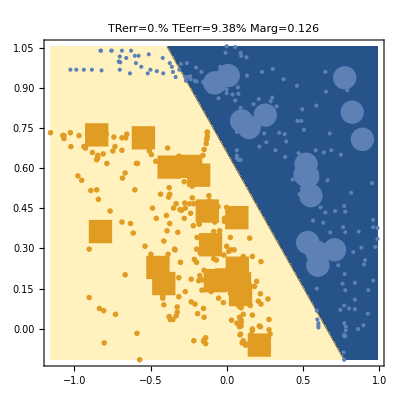

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[10];
results=runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainMaxMargin]
```

```mathematica
getTrTeData[trPerc_]:=Module[{lab,feat,yTr,fTr,yTe,fTe,trSet,nSamp},
lab=Flatten[{Table[{1.},{Length[xPos]}],Table[{-1.},{Length[xNeg]}]},1];
feat=Flatten[{xPos,xNeg},1];
nSamp=Length[lab];
SeedRandom[12345];
trSet=Table[Boole[RandomReal[]>(100-trPerc)/100],{i,1,nSamp}];
fTr=feat[[Flatten@Position[trSet,1],All]];
yTr=lab[[Flatten@Position[trSet,1]]];
fTe=feat[[Flatten@Position[trSet,0],All]];
yTe=lab[[Flatten@Position[trSet,0]]];
{fTr,yTr,fTe,yTe}
];
```

```mathematica
runMaxMarginExperiment[fTr_List,yTr_List,fTe_List,yTe_List,classifier_]:=Module[
{model,margin,teResults,trResults},
{model,margin}=classifier[fTr,yTr];
trResults=testMaxMargin[model,fTr,yTr];
teResults=testMaxMargin[model,fTe,yTe];
plotLinearResults[testMaxMargin,model,fTr,yTr,fTe,yTe,(1-trResults[[1]])*100,(1-teResults[[1]])*100,margin]
];
```

```mathematica
plotLinearResults[testFunc_,model_,fTr_List,yTr_List,fTe_List,yTe_List,trErr_Real,teErr_Real,margin_Real]:=Module [
{f1,f2,posTr,negTr,posTe,negTe,minP,maxP,a,b,c},
posTr=Transpose[MatrixForm[Position[yTr,1.]]][[All,1]][[1]];
negTr=Transpose[MatrixForm[Position[yTr,-1.]]][[All,1]][[1]];
posTe=Transpose[MatrixForm[Position[yTe,1.]]][[All,1]][[1]];
negTe=Transpose[MatrixForm[Position[yTe,-1.]]][[All,1]][[1]];
a=ListPlot[{fTr[[negTr]],fTr[[posTr]]},PlotRange -> Full,PlotMarkers->{Automatic,24}];
c=ListPlot[{fTe[[negTe]],fTe[[posTe]]},PlotRange -> Full];
f1=Join[fTr[[All,1]],fTe[[All,1]]];
f2=Join[fTr[[All,2]],fTe[[All,2]]];
b=ContourPlot[testFunc[model,{{x,y}},{{1}}][[3]],{x,Min[f1],Max[f1]},{y,Min[f2],Max[f2]},Contours->{0},PlotPoints->4];
Show[b,a,c,ImageSize->plotSize, PlotLabel ->Style[ StringJoin[{"TRerr=", ToString[NumberForm[trErr,3]],"% TEerr=", ToString[NumberForm[teErr,3]], "% Marg=", ToString[NumberForm[margin,3]]}], FontSize -> 21]]
];
```

### Max-margin classifier: soft margin

the max-margin formulation is for linearly separable problems only

on non linearly-separable problems: no feasible solution

idea: allow the algorithm to violate the constraints by an amount ξ_i, as little as possible

min_(w,b,ξ) w·w +C ∑_(i=1)^n ξ_i
s.t. y_i(w·x_i+b)≥1-ξ_i,   i=1,…,n,
          ξ_i≥0,                                  i=1,…,n

C is an Hyper-parameter of the function
it tunes the importance of the minimization of the ξ_i

big value of C will force all the points to be correctly classified with margin 1 (if possible)

low value of C will allow for lower or even negative margin on some samples

### Max-margin classifier: soft margin (code)

still a short QP

```mathematica
trainSoftMargin[fTr_List,yTr_List,regC_]:=Module[
{results,model,margin,nTr,fTr2,d,w,v,b,xi,x,i,sol,obj,cnstr},
{nTr,d}=Dimensions[fTr];
w=Table[Subscript[v, i],{i,d}];
xi=Table[Subscript[x, i],{i,nTr}];
cnstr=And@@(#<=0&/@Flatten@(1-xi-(fTr.w+b)yTr))
&& And@@(#>=0&/@Flatten@xi);
obj=w.w+regC Total[xi];
sol=FindMinimum[{obj,cnstr},Join[w,{b},xi], Compiled->True, 
Method -> "QuadraticProgramming"];
model=({w,b,xi}/.sol[[2]]);
margin=(1-Max[model[[3]]])/Norm[model[[1]]];
results={model,margin}
];
```

### Max-margin classifier: soft margin (demo)

use the function createData to draw an arbitrary training set as you wish

after calling this createData, it is possible to draw samples in the plot simply by clicking and dragging

a single click in any point of the plot will change the color/label of the samples that are going to be drawn subsequently

```mathematica
createData[]
```

-Graphics-

runMaxMarginExperiment[fTr,yTr,fTe,yTe] to train and test the algorithm on the data

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[10];
Manipulate[runMaxMarginExperiment[fTr,yTr,fTe,yTe,trainSoftMargin[#1,#2,10^c]&],{c,0,5,.2}]
```

```mathematica
Export["ML3_data.mat",{fTr, yTr, fTe,yTe}]
```

ML3_data.mat

## Section. Support Vector Machines (SVM)

SVMs are max-margin classifiers, optimized in a different way

### Hard-margin SVM

Given the optimization problem for the max-margin classifier

min_(w,b) w·w
s.t. 1-y_i(w·x_i+b)≤0,   ∀(x_(i,)y_i)∈S

its generalized Lagrangian is given by

L(w,b,α)=1/2(‖w‖)^2 + ∑_(i=1)^n α_i(1-y_i(w·x_i+b))

### Hard-margin SVM (optimality conditions)

Lagrangian dual problem, equivalent to the original problem is defined as

max_α inf_(w,b) 1/2(‖w‖)^2 + ∑_(i=1)^n α_i(1-y_i(w·x_i+b))
s.t. α≥0

optimality conditions:

(∂L(w,b,α))/(∂w)=0 ⟶ w=∑_(i=1)^n α_i y_i x_i
(∂L(w,b,α))/(∂b)=0 ⟶ ∑_(i=1)^n α_i y_i=0
α_i(1-y_i(w·x_i+b))=0,     i=1,…,n      (Complementarity Condition)

Support Vectors: { x_i:  y_i(w·x_i+b)=1 }

only the closest points to the classification hyperplane become Support Vectors

### Hard-margin SVM (dual problem)

plugging the solution for w back into the Lagrangian, the dual problem becomes

max_{α} 1ᵀα-1/2 αᵀHα
s.t. α≥0
	αᵀy=0

where H_(i,j)=y_i y_j x_i·x_j

it still has the form of a convex Quadratic Programming (QP) problem

only Support Vectors contribute to the prediction

f_(w,b)(x_i)=w·x +b=∑_(j=1)^n α_j y_j x_j·x_i+b

### Hard-margin SVM (code)

SVM: a quadratic program, with simple constraints

KTr is the matrix of inner products Ktr_(i,j)=x_i·x_j computed using the training samples

```mathematica
trainHardMarginSVM[KTr_,yTr_]:=Module[
{nTr,d,H,f,a,alpha,b,margin,sol,obj,constraints},
{nTr,d}=Dimensions[KTr];
f=Table[1,{i,nTr}];
alpha=Table[Subscript[a, i],{i,nTr}];
H=yTr.Transpose[yTr] KTr;
constraints=First[alpha.yTr]==0 && (#>=0&/@(And@@alpha));
obj=1/2 alpha.H.alpha - f.alpha;
sol=FindMinimum[{obj,constraints},alpha, Compiled->True, 
AccuracyGoal->1, PrecisionGoal->1, MaxIterations->100,
Method -> "QuadraticProgramming", Gradient:> H.alpha -f];
alpha=(alpha/.sol[[2]]);
alpha[[Flatten@Position[#<10^(-8)&/@alpha,True]]]=0;
b=-1/Total[alpha] (alpha yTr[[All,1]]).H.alpha;
margin=Total[alpha]^(-1/2);
alpha=alpha yTr[[All,1]];
{{alpha,b},margin}];
```

```mathematica
linearKernel[fTr_,fTe_]:=Module[{K},
K=fTr.Transpose[fTe]
];
```

```mathematica
testSVM[model_,KTe_,yTe_]:=Module[
{nTe,nTr,a,b,pred,score,correct},
a=model[[1]];
b=model[[2]];
{nTe,nTr}=Dimensions[KTe];
score=Flatten[KTe.a+b];
pred=Sign[score];
correct=Count[#>0&/@(score yTe[[All,1]]),True]/Length[yTe]//N;
{correct,pred,score}
];
```

### Hard-margin SVM (demo)

use the function createData to draw an arbitrary training set as you wish

after calling this createData, it is possible to draw samples in the plot simply by clicking and dragging

a single click in any point of the plot will change the color/label of the samples that are going to be drawn subsequently

```mathematica
createData[]
```

-Graphics-

Support Vectors are marked with thicker markers

only the closest points to the classification hyperplane become Support Vectors

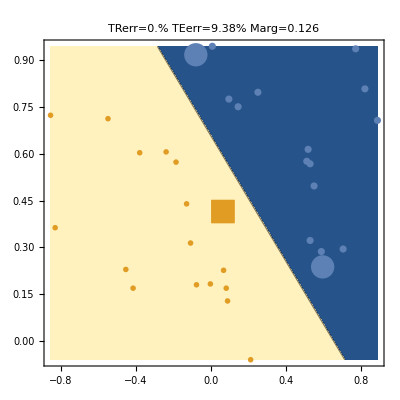

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[10];
runSVMExperiment[fTr,yTr,fTe,yTe,trainHardMarginSVM,linearKernel]
```

```mathematica
runSVMExperiment[fTr_List,yTr_List,fTe_List,yTe_List,classifier_,kernFunc_]:=Module[
{KTr,model,margin,nTr,trResults,teResults},
KTr=kernFunc[fTr,fTr];
{model,margin}=classifier[KTr,yTr];
trResults=testSVM[model,KTr,yTr];
teResults=testSVM[model,kernFunc[fTe,fTr],yTe];
plotKernelResults[model,fTr,yTr,fTe,yTe,kernFunc,(1-trResults[[1]])*100,(1-teResults[[1]])*100,margin]
];
```

```mathematica
plotKernelResults[model_,fTr_,yTr_,fTe_,yTe_,kernelFunc_,trErr_,teErr_,margin_]:=Module [
{sv,posTe,negTe,pos,posSV,negSV,posAll,negAll,fnSV,fpSV,neg,minP,maxP,a,b,c,d},
sv=Boole[#>0]&/@(model[[1]] Flatten@yTr);
pos=Boole[#>0]&/@Flatten@yTr;
posSV=Transpose[MatrixForm[Position[(sv pos),1]]][[All,1]][[1]];
negSV=Transpose[MatrixForm[Position[(sv (1-pos)),1]]][[All,1]][[1]];
posAll=Transpose[MatrixForm[Position[pos,1]]][[All,1]][[1]];
negAll=Transpose[MatrixForm[Position[(1-pos),1]]][[All,1]][[1]];
fnSV=fTr[[negSV]];
fpSV=fTr[[posSV]];
fnSV=If[Length[fnSV]==0,{{Null,Null}},fnSV];
fpSV=If[Length[fpSV]==0,{{Null,Null}},fpSV];
a=ListPlot[{fnSV,fpSV},PlotRange -> Full,PlotMarkers->{Automatic,24}];
b=ListPlot[{fTr[[negAll]],fTr[[posAll]]},PlotRange -> Full];
d=ContourPlot[First[(kernelFunc[{{x,y}},fTr]).model[[1]]+model[[2]]],{x,Min[fTr[[All,1]]],Max[fTr[[All,1]]]},
{y,Min[fTr[[All,2]]],Max[fTr[[All,2]]]},Contours->{0},PlotPoints->50];
Show[d,a,b,ImageSize->plotSize, PlotLabel ->Style[ StringJoin[{"TRerr=", ToString[NumberForm[trErr,3]],"% TEerr=", ToString[NumberForm[teErr,3]], "% Marg=", ToString[NumberForm[margin,3]]}], FontSize -> 21]]
];
```

## Section. Kernel Support Vector Machines

### Non-linear Mappings

Linear-threshold algorithms can only learn linear classifiers

often data is not linearly separable

idea: non-linearly map the vectors x_i ∈ X into a new Feature Space φ(x_i ) ∈ F

samples become linearly separable in F

-Graphics-

### Kernel Methods

Kernel methods allow to perform the mapping

without  explicitly defining the feature space F

without explictly performing the mapping

#### Kernel function

A function k(·, ·) that for all x, z ∈ X satisfies

k(x, z) = φ(x)· φ(z),

where φ : x → φ(x) ∈ F is a mapping from X to an Hilbert space F

with φ(x) = x, the simplest example of kernel function: k(x, z) = x·z

#### Constructing kernels.

Let k_1, k_2 and k_3 be kernel functions, a∈ℝ^+, f(·) a real function, ϕ:X→ℝ^m, and B a symmetric p.s.d. matrix. The following functions are also kernels:

k(x,z)=k_1(x,z)+k_2(x,z),
k(x,z)=ak_1(x,z),
k(x,z)=k_1(x,z)k_2(x,z),
k(x,z)=f(x)f(z),
k(x,z)=k_3(ϕ(x),ϕ(z)),
k(x,z)=xᵀBz

Combining these functions:

k(x,z)=p(k_1(x,z))                                               (Polynomial kernel),
k(x,z)=exp(k_1(x,z))                                           (Exponential kernel),
k(x,z)=exp(-1/σ^2(‖x-z‖)^2)             (Gaussian kernel)

### Kernel Support Vector Machines

max_{α} 1ᵀα-1/2 αᵀHα
s.t. α≥0
	αᵀy=0

the SVM the training procedure depends on data only via the inner products of the training instances, encoded in the matrix H_(i,j)=y_i y_j x_i·x_j.

substitute inner products x_i·x_j in H, with evaluations of a kernel function k(x_i,x_j)

H_(i,j)=y_i y_j k(x_i·x_j)

during prediction we have:

f_(w,b)(x_i)=w·x +b=∑_(j=1)^n α_j y_j k(x_j,x_i)+b,

### Kernel Methods (code)

Efficient computation of the Gaussian kernel (without any loop on the samples)

```mathematica
computeGaussianKernel[fTr_,fTe_,sigmaSQ_]:=Module[{D,K},
D=computeDist[fTr,fTe];
K=Exp[-1/(2 sigmaSQ) D]
];
```

```mathematica
computeDist[fTr_,fTe_]:=Module[{d,nTr,nTe,NTr,NTe,P,D},
{nTr,d}=Dimensions[fTr];
{nTe,d}=Dimensions[fTe];
P=fTr.Transpose[fTe];
NTr=Transpose[Table[Norm/@fTr, {i,nTe}]];
NTe=Table[Norm/@fTe, {i,nTr}];
D=NTr+NTe-2P
];
```

### Kernel Methods (demo)

use the function createData to draw an arbitrary training set as you wish

after calling this createData, it is possible to draw samples in the plot simply by clicking and dragging

a single click in any point of the plot will change the color/label of the samples that are going to be drawn subsequently

```mathematica
createData[]
```

-Graphics-

example using a Gaussian kernel with the 1-norm soft-margin SVM

the linearKernel function has been replaced with the gaussianKernel (σ automatically estimated)

```mathematica
{fTr,yTr,fTe,yTe}=getTrTeData[30];
Manipulate[runSVMExperiment[fTr,yTr,fTe,yTe,train1NormSoftMarginSVM[#1,#2,10^c]&,gaussianKernel[fTr]],{c,0,6,0.5}]
```

```mathematica
gaussianKernel[input_]:=Module[{sigmaSQ,slack,myGaussianKern},
sigmaSQ=If[Length[input]>1,estimateSigmaSQ[input],input];
myGaussianKern[x_,y_]:=computeGaussianKernel[x,y,sigmaSQ];
myGaussianKern
];
```

```mathematica
estimateSigmaSQ[fTr_]:=Module[{sigmaSQ,D},
D=computeDist[fTr,fTr];
sigmaSQ=Mean[Mean[D]]
];
```

```mathematica
Export["ML3_data.mat",{fTr, yTr, fTe,yTe}]
```

ML3_data.mat

## Section. Conclusion

the notebook presents several max-margin and SVM classifiers

both in the linear and non-linear setting

it exploits the Quadratic Programming solver of Mathematica to implement most of the proposed the algorithms

dynamic interactions, as dataset drawing and direct manipulation of the algorithm hyper-parameters

the implementations provided could virtually be used to address any binary classification problem

for larger scale problems:

implement a Mathematica interfaces to existing specialized and efficient C++ SVM implementations

experiment with (stochastic) gradient descent, e.g. using the FixedPoint[] Mathematica funcitonality

## References

1.	Nello Cristianini and John Shawe-Taylor. An introduction to Support Vector Machines and other kernel-based learning methods. Cambridge university press, 2000